```mathematica
Guy F. Mongelli                        11/3/2012
Prof. J. Adin Mann       ECHE 475
```

```mathematica
Midterm Take Home Problem Set
```

```mathematica
Problem 1
```

```mathematica
Part A:
```

```mathematica
The following is a parametrically defined vector function (Rank 1).  The parameter variable, t, is varied in the domain of [0,π/2].  Therefore the codomain of x is identically [0,π/2].The codomain of y is [0,1].  The x and x components of this parameterized function is continuous on the domain of t ( and even in extended domains of [-∞,∞]).  It is also infinitely differentiable in the bounded and infinite limits of t. The x component will have issues after the first derivative because the function will be undefined as all of the y values will be mapped onto the x=0 ordinate. Because of their defferentiability properties, they are also square integrable functions.
```

```mathematica
y1=({{t}, {(Sin[t])^2}})
```

{{t},{Sin[t]^2}}

```mathematica
N[Pi/2,3]
```

1.57

```mathematica
FindMaximum[(Sin[t])^2,t]
```

{1.,{t→1.5708}}

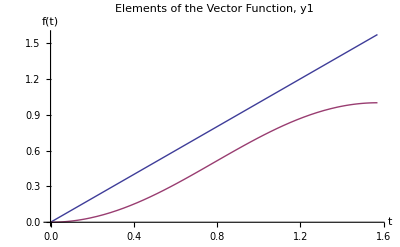

```mathematica
Plot[{t,(Sin[t])^2},{t,0,Pi/2},PlotLabel->"Elements of the Vector Function, y1",AxesLabel->{t,f[t]}]
```

```mathematica
For interest, the legnth of the vector as a function of time is:
```

```mathematica
dist[t_]=Sqrt[t^2+(Sin[t])^4]
```

√(t^2+Sin[t]^4)

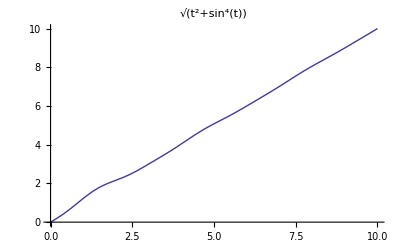

```mathematica
Plot[dist[t],{t,0,10},PlotLabel->dist[t]]
```

```mathematica
dist[Pi/2]
```

√(1+π^2/4)

```mathematica
N[dist[Pi/2],3]
```

1.86

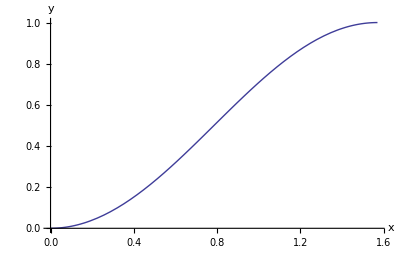

```mathematica
ParametricPlot[{t,(Sin[t])^2},{t,0,Pi/2},AxesLabel->{x,y}]
```

```mathematica
Manipulate[ParametricPlot[{t^n
,(Sin[t])^2},{t,0,Pi/2},PlotRange->{0,1},AxesLabel->{x,y}],{n,1,2,3,4,5}]
```

```mathematica
The following function is a scalar function (Rank 0 tensor).  The domain is from [0,1].  The codomain is from [0,1]. The function is continuous over the domain and extended domain.  The function is smooth and infinitely differentiable .  It is also square integrable.
```

```mathematica
y2=x^2
```

x^2

```mathematica
The domain of this function is [0,1] and the codomain is [0,1].
```

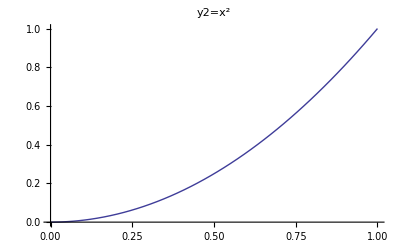

```mathematica
Plot[y2,{x,0,1},PlotLabel->"y2=x^2"]
```

```mathematica
Part B:
```

```mathematica
Strange[x_]=(Sin[x]+Cos[x]+Exp[x])/Log[1+x^2]
```

(ⅇ^x+Cos[x]+Sin[x])/Log[1+x^2]

```mathematica
Strange[0]
```

Power::infy: Infinite expression 1/0 encountered.

ComplexInfinity

```mathematica
The function is not defined at the origin, otherwise the limit would be simple to compute.  Because the function goes to zero over zero, it is possible to apply L'Hospotal's Rule.  This Rule indicates that the limit of the function can be evaluated by observing the limit of the ratio of the derivatives of the numerator and denominator (sans Product/Quotient Rule).
```

```mathematica
D[(Sin[x]+Cos[x]+Exp[x])/Log[1+x^2],x]
```

(ⅇ^x+Cos[x]-Sin[x])/Log[1+x^2]-(2 x (ⅇ^x+Cos[x]+Sin[x]))/((1+x^2) Log[1+x^2]^2)

```mathematica
For interest into the true derivative of the function, it is computed here, although it does not assist in solving this problem.
```

```mathematica
Expand[D[(Sin[x]+Cos[x]+Exp[x])/Log[1+x^2],x]]
```

-(2 ⅇ^x x)/((1+x^2) Log[1+x^2]^2)-(2 x Cos[x])/((1+x^2) Log[1+x^2]^2)+ⅇ^x/Log[1+x^2]+Cos[x]/Log[1+x^2]-(2 x Sin[x])/((1+x^2) Log[1+x^2]^2)-Sin[x]/Log[1+x^2]

```mathematica
Full Simplify[D[(Sin[x]+Cos[x]+Exp[x])/Log[1+x^2],x]]
```

1/(Log[1+x^2]^2)Full (Log[1+x^2] (ⅇ^x+Cos[x]-Sin[x])-(2 x (ⅇ^x+Cos[x]+Sin[x]))/(1+x^2))

```mathematica
Limit[D[(Sin[x]+Cos[x]+Exp[x])/Log[1+x^2],x],x->0]
```

-∞

```mathematica
Finally, the L'Hospital derivative is computed.
```

```mathematica
D[Sin[x]+Cos[x]+Exp[x],x]/D[Log[1+x^2],x]
```

((1+x^2) (ⅇ^x+Cos[x]-Sin[x]))/(2 x)

```mathematica
Expand[D[Sin[x]+Cos[x]+Exp[x],x]/D[Log[1+x^2],x]]
```

ⅇ^x/(2 x)+(ⅇ^x x)/2+Cos[x]/(2 x)+1/2 x Cos[x]-Sin[x]/(2 x)-1/2 x Sin[x]

```mathematica
FullSimplify[D[Sin[x]+Cos[x]+Exp[x],x]/D[Log[1+x^2],x]]
```

((1+x^2) (ⅇ^x+Cos[x]-Sin[x]))/(2 x)

```mathematica
Limit[D[Sin[x]+Cos[x]+Exp[x],x]/D[Log[1+x^2],x],x->0]
```

∞

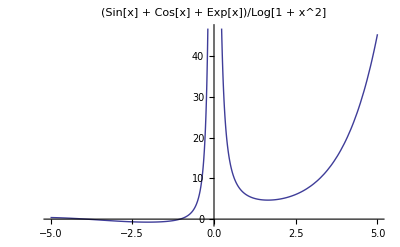

```mathematica
Plot[(Sin[x]+Cos[x]+Exp[x])/Log[1+x^2],{x,-5,5},PlotLabel->"(Sin[x] + Cos[x] + Exp[x])/Log[1 + x^2]"]
```

```mathematica
Limit[(Sin[x]+Cos[x]+Exp[x])/Log[1+x^2],x->0]
```

∞

```mathematica
The left-hand limit is:
```

```mathematica
Limit[(Sin[x]+Cos[x]+Exp[x])/Log[1+x^2],x->0,Direction->1]
```

∞

```mathematica
The right-hand limit is:
```

```mathematica
Limit[(Sin[x]+Cos[x]+Exp[x])/Log[1+x^2],x->0,Direction->-1]
```

∞

```mathematica
Looking at a plot of this function and evaluating the left and right hand limits indicated that the limit diverges to positive infinity (does not exist).  This comes from the misbehavior of the logarithm in the denominator around x=0.
```

```mathematica
<<PlotLegends`
```

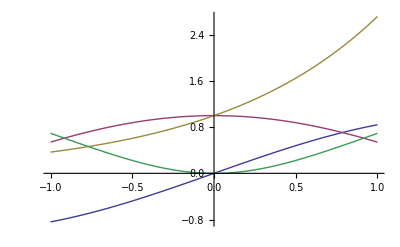

```mathematica
Plot[{Sin[x],Cos[x],Exp[x],Log[1+x^2]},{x,-1,1},PlotLegend->{"Sin[x]","Cos[x]","Exp[x]","Log[1+x^2]"}]
```

```mathematica
Part C:
```

```mathematica
The infinite product can be rewritten as:
```

```mathematica
∏_(n=1)^∞ (2n-1)/(2n)
```

0

```mathematica
The correct way to discuss the infinite product in this context is to say that the infinite product diverges to zero.
```

```mathematica
To understand why this is the case, a careful examination of the value of each term is required.  The integer values are the most critical.  The funcion starts by generating (1/2) and multiplying it by (3/4), then (5/6) then (7/8). and so on.
```

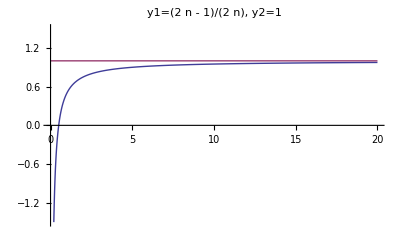

```mathematica
Plot[{(2n-1)/(2n),1},{n,0,20},PlotRange->{-1.5,1.5},PlotLabel->"y1=(2  n - 1)/(2  n), y2=1" ]
```

```mathematica
A method to rewrite the infinite product of a certain number of terms is to recall the gamma function.  Relating the gamma function to the infinte product is fascinating because it reiterates the connection of the integral convergence tests for series.  This infinite product can be rewritten as an infinite series.
```

```mathematica
f[x_]=∏_(n=1)^x (2n-1)/(2n)
```

Gamma[1/2+x]/(√π Gamma[1+x])

```mathematica
When each term is multiplied by successive terms which are larger, the number decreases and in the infinte limit goes to zero.  This sysstem is analogous to the problem of being 1 foot away from the wall and sequentially taking steps equal to half of the distance remaining from you to the wall to get to the wall.  In any finite limit, it seems that you will never reach the wall, however in the infinite limit, you do.  This infinite product represents the same problem by using multiplication to relate the distance you step as a certain fraction of the distance of the last step.  These steps are getting smaller and smalle, as the distance from the final destination gets smaller and smaller as well.  In essence it tells you how far you are from the origin and tells you how far you have left. In this example the distance stepped is not the same fraction of the distance taken in the last step. Another way to think about it is to consider that even though the numbers multiplied in each term are getting larger, there are an infinite number of fractions less than on ebeing mutiplied by one another. It is not terribly surprising, then that the product of this infinite set of numbers is close enought to zero to call it just that.
```

```mathematica
Limit[Gamma[1/2+x]/(√π Gamma[1+x]),x->∞]
```

0

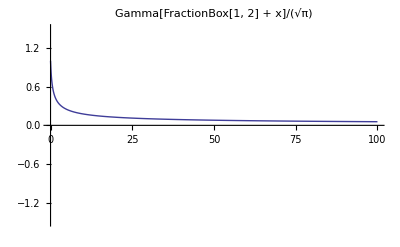

```mathematica
Plot[Gamma[1/2+x]/(√π Gamma[1+x]),{x,0,100},PlotRange->{-1.5,1.5},PlotLabel->"Gamma[FractionBox[1, 2] + x]/(√π)"]
```

```mathematica
The convergence criteria for the infinite product will be that the infinite product of a series term denoted a[n] will converge if and only of the infinite series of the logarithm of a[n] with base ten converges.
```

```mathematica
∑_(n=1)^∞ Log[(2n-1)/(2n)]
```

Sum::div: Sum does not converge.

∑_(n=1)^∞ Log[(-1+2 n)/(2 n)]

```mathematica
∑_(n=1)^∞ Log[10,(2n-1)/(2n)]
```

Sum::div: Sum does not converge.

∑_(n=1)^∞ Log[(-1+2 n)/(2 n)]/Log[10]

```mathematica
Since these inifinite series do not converge, we would expect the appropriate manipulation of the infinite product not to converge.
```

```mathematica
In the infinite limit, each successive multiplication step is multiplying by a number that is approxamately 1.
```

```mathematica
Limit[(2n-1)/(2n),n->∞]
```

1

```mathematica
In the infinite series case, each term essentially adds zero to the total sum.
```

```mathematica
Limit[Log[(2n-1)/(2n)],n->∞]
```

0

```mathematica
Limit[(2n-1)/(2n),n->0]
```

-∞

```mathematica
Limit[(2n)/(2n+1),n->0]
```

0

```mathematica
Limit[Log[(2n+1)/(2n)],n->0]
```

∞

```mathematica
Problem 2:
```

```mathematica
Part A:
```

```mathematica
The function is plotted before the limit is evaluated.The existence of the function at the point in the limit of evaluation exists.  Since the right hand and left hand limits exist and equal the same value, the limit is said to exist and go to 1.
```

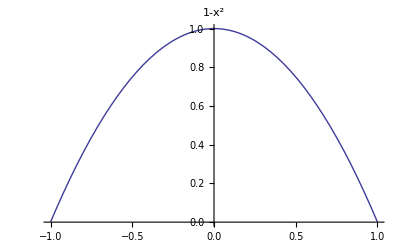

```mathematica
Plot[1-x^2,{x,-1,1},PlotLabel->"1-x^2"]
```

```mathematica
Limit[1-x^2,x->0]
```

1

```mathematica
Limit[1-x^2,x->0,Direction->1]
```

1

```mathematica
Limit[1-x^2,x->0,Direction->-1]
```

1

```mathematica
Part B:
```

```mathematica
The function is plotted.  This goes back to the notion of taking steps toward an wall a certain fixed distance away, where the legnth of the step is proportional to either the distnace travelled or to the distance remaining.  These cases will show that the relationship between the distance taken in a step to the distance travelled, the distance taken in the last step or the distance remaining is not the same.
```

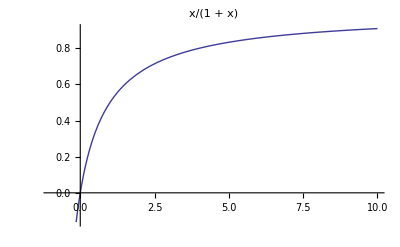

```mathematica
Plot[x/(1+x),{x,-1,10},PlotLabel->"x/(1 + x)"]
```

```mathematica
The function does not posses and discontinuities, lack of smoothness or other misbehavior that would indicate that its limit does not exist. The plot above shows readily that the limit is 1.
```

```mathematica
Limit[x/(1+x),x->∞]
```

1

```mathematica
Part C:
```

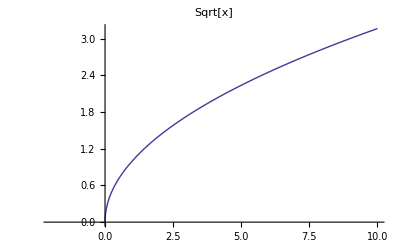

```mathematica
Plot[Sqrt[x],{x,-2,10},PlotLabel->"Sqrt[x]"]
```

```mathematica
The function is plotted above, and is not definted in the real plane for negative values.  The right hand limit is obviously zero, however, the left hand limit is non-obviously zero, and the limit is actually zero.  The problem in part D is more confusing, at least initially, because it also involves square roots in domains that lie along the complex plane.
```

```mathematica
(* THIS FUNCTION STILL REQURIES WORK It shouw that complex part evaporating around the origin and becoming a line instead of a surface.  Work to get it right.*)
```

```mathematica
ParametricPlot3D[{Re[Sqrt[x]],Im[Sqrt[x]],0},{x,-5,5},AxesLabel->{z,Re[Sqrt[x]],Im[Sqrt[x]]}]
```

-Graphics3D-

```mathematica
Limit[Sqrt[x],x->0]
```

0

```mathematica
Limit[Sqrt[x],x->0,Direction->1]
```

0

```mathematica
Limit[Sqrt[x],x->0,Direction->-1]
```

0

```mathematica
Part D:
```

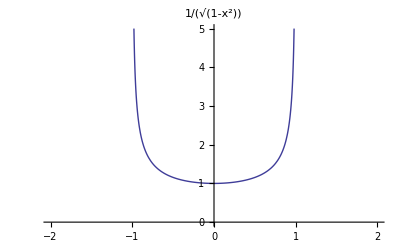

```mathematica
Plot[(1-x^2)^(-1/2),{x,-2,2},PlotLabel->(1-x^2)^(-1/2),PlotRange->{0,5}]
```

```mathematica
Mathematica indicates that the limit is complex infiniti, even though obsercation of the function seems to lead to the conclusion that the limit should converge to one.
```

```mathematica
Limit[(1-x^2)^(-1/2),x->1]
```

(-ⅈ) ∞

```mathematica
Looking at the left-hand and right-hand limits are not encouraging and suggest that the limit does not exist since they are unequal (complex infinit and real infiniti, respectively)
```

```mathematica
Limit[(1-x^2)^(-1/2),x->1,Direction->1]
```

∞

```mathematica
Limit[(1-x^2)^(-1/2),x->1,Direction->-1]
```

(-ⅈ) ∞

```mathematica
Maybe a L'Hospital's-type Rule will help..
```

```mathematica
D[(1-x^2)^(-1/2),x]
```

x/((1-x^2)^(3/2))

```mathematica
Limit[x/((1-x^2)^(3/2)),x->0]
```

0

```mathematica
D[(1-x^2)^(-1/2),{x,2}]
```

(3 x^2)/((1-x^2)^(5/2))+1/((1-x^2)^(3/2))

```mathematica
Limit[D[(1-x^2)^(-1/2),{x,2}],x->0]
```

1

```mathematica
D[(1-x^2)^(-1/2),{x,3}]
```

(15 x^3)/((1-x^2)^(7/2))+(9 x)/((1-x^2)^(5/2))

```mathematica
L'Hospitals-type rules do not seem to help..Not that we expected them to. Regardless of what the left-hand and right-hand limits computed in Mathematica indicate, it appears that the limit should go to 1.
```

```mathematica
Limit[D[(1-x^2)^(-1/2),{x,3}],x->1]
```

ⅈ ∞

```mathematica
Problem 3:
```

```mathematica
The following function, denoted here as f, describes the fraction of surface coverage and is referred to as the Langmuir isotherm and comes about from solving the Hill-Landmuir equation. It is a specific case of an ideal-lattice-gas equation (Intro. to Chem. Eng. Thermodynamics by Smith, van Ness and Abbott). An alternative to this equation is the Freundlich equation. Langmuir isotherms can be derived from equilibrium kinteics of filled and unfilled sites as a function of the adsorption constant,a.  This constant essentially specifies the stability of the system that is gained by adsorbing a molecule.  The isotherm denotes the fraction of sites filled at a given temperature as a function of the system pressure (partial or total) or concentration.  The stability could be in terms of Gibb's Free Energy or other parameters, but the need to fill sites will be driven by the energy available at a certain temperature.  The value of a increases with the binding energy of the particle adsorbed onto the site and with decreasing T.
```

```mathematica
The Langmuir isotherm can also be derived from a Statistical Mechanics ensamble of m sites with n particles as a function of temperature.The temperature dependence likely has an equilibrium or rate constant controlled by a Boltzman, exponential of the binding energy and temperature.
```

```mathematica
f[x_]=(a*x)/(1+a*x)
```

(a x)/(1+a x)

```mathematica
f[a_,x_]=(a*x)/(1+a*x)
```

(a x)/(1+a x)

```mathematica
f[0,1]
```

0

```mathematica
f[1,0]
```

0

```mathematica
f[1,1]
```

1/2

```mathematica
Plot3D[f[a,x],{a,0,5},{x,0,5},AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
The codomain of this function as a function of a is given by [0,∞].
```

```mathematica
For a specific upper bound of the function at a given pressure or concentration, see the following line of code.
```

```mathematica
Manipulate[f[a,x],{x,0,10}]
```

```mathematica
This plot establishes the upper bound on f for a given a value of x and is implied by the curve above.
```

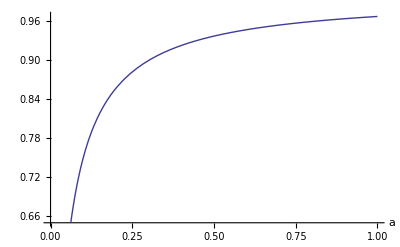

```mathematica
Plot[f[a,30],{a,0,1},AxesLabel->Automatic]
```

```mathematica
The codomain of a is indeed a subset of ℜ, since ℜ includes all real numbers (including positives, negatives, zero, rationals and irrationals).
```

```mathematica
For personal curiosity the first derivatives with respect to a and x are calculated.
```

```mathematica
D[(a x)/(1+a x),x]
```

-(a^2 x)/(1+a x)^2+a/(1+a x)

```mathematica
D[(a x)/(1+a x),a]
```

-(a x^2)/(1+a x)^2+x/(1+a x)

```mathematica
Part B:
```

```mathematica
In the zero limit, the value of f goes to zero.  This means, simply, that as the partial/total pressure of the system goes to zero, that the fraction of filled sites goes to zero as well.
```

```mathematica
Limit[f[x],x->0]
```

0

```mathematica
Part C:
```

```mathematica
As the pressure or concentration of a species in solution gets very very high, all of the sites will be filled so the fraction of sites filled would be 1.  This is the case of full monolayer coverage.  There are other forms of the Langmuir isotherm that have saturation values less than one as related to the Henry's Law constant or other laws (Toth equation,
```

```mathematica
Limit[(a*x)/(1+a*x),x->∞]
```

1

```mathematica
Part D:
```

```mathematica
The inverse function is defined such that when the function and its inverse are applied to one another in each order, the identity element, x, is output.
```

```mathematica
Testing a trial inverse function to see if it rearranges appropriately.
```

```mathematica
Solve[y==x/(a(1-x)),x]
```

{{x→(a y)/(1+a y)}}

```mathematica
Solving for the inverse function from the original function:
```

```mathematica
Solve[y==f[x],x]
```

{{x→-y/(a (-1+y))}}

```mathematica
finv[x_]=x/(a(1-x));
```

```mathematica
Applying the function and its inverse to themselves in sequential orderings:
```

```mathematica
FullSimplify[finv[f[x]]]
```

x

```mathematica
FullSimplify[f[finv[x]]]
```

x

```mathematica
This function passes all of the tests for an inverse function.
```

```mathematica
Part E:
```

```mathematica
f is continuous and infinitely differentiable with respect to x and a over the domain of [0,∞].Since negative pressures and concentrations do not make physical sense for the sytem of interest, they have been neglected from the domin.
```

```mathematica
Part F:
```

```mathematica
It is not clear that this integral has any physical meaning other than being the area under the curve of the function given, which is not the same as the integral of the Langmuir isotherm!  This is however, useful, in cmoputing the spreading pressure, ∏.  (* See p. 610 to interrelate that calculation to this one. *)
```

```mathematica
∫_0^(a*x) z/(1+z)ⅆz
```

ConditionalExpression[a x-Log[1+a x],Re[1/(a x)]≥0||Re[1/(a x)]≤-1||1/(a x)∉Reals]

```mathematica
This integral gives a count of all of the fraction of sites that have been occupied as the pressure or concentration increases to a certain value from no sites occupied.
```

```mathematica
∫_0^x (a*z)/(1+a*z)ⅆz
```

ConditionalExpression[(a x-Log[1+a x])/a,Re[1/(a x)]≥0||Re[1/(a x)]≤-1||1/(a x)∉Reals]

```mathematica
func[x_,a_]=a *x-Log[1+a* x]
```

a x-Log[1+a x]

```mathematica
Plot3D[func[x,a],{x,0,100},{a,0,1},AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
Limit[func[x],x->0]
```

0

```mathematica
Problem 4:
```

```mathematica
Clear[n]
```

```mathematica
This entropy fundamental equation is not for an ideal gas, which scales as the Log[V/N] and the Log[U^(3/2)].  This can also be rewritten in terms of temperature.  Based  upon the differential form given, chemical potential is not a factor, otherwise there would have been a sum over the number of particles (as it would be in a more complete/realistic ensamble).  Therefore, it is assumed that the number of particles is held constant (if it weren't then then Subscript[((∂S)/(∂N)), V,E]=-μ/T).
```

```mathematica
S=(R^2/(θ*Subscript[υ, 0]))(n*V*U)^(1/3);
```

```mathematica
S^3
```

(n R^6 U V)/(θ^3 υ_0^3)

```mathematica
D[(R^2/(θ*Subscript[υ, 0]))(n*V*U)^(1/3),V]
```

(n R^2 U)/(3 (n U V)^(2/3) θ υ_0)

```mathematica
Problem 5:
```